```mathematica
f[x_,y_,r_]:=x^2+y^2-r^2
```

```mathematica
fr[r_,al_]:={r Cos[al+Pi/2],r Sin[al+Pi/2]}
```

```mathematica
df[{x_,y_,r_}]:=√(r^2-x^2)+x/y
```

```mathematica
fr[4.,Pi]
```

{-4.,0.}

```mathematica
df[Flatten[{fr[4.,Pi*0.0001],4}]]
```

3183.1

```mathematica
ArcTan[%]
```

1.32582

```mathematica
Pi/6.
```

0.523599

```mathematica
yx[x_,r_]:=√(r^2-x^2)
```

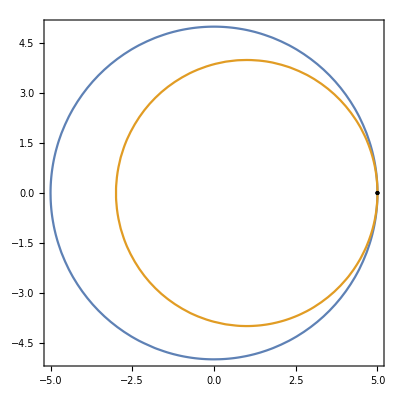

```mathematica
ContourPlot[{f[x,y,5]==0,f[x-1,y,4]==0},{x,-5,5},{y,-5,5},Epilog->Point[point/.{a->5}]]
```

```mathematica
point= {x,y}/.Solve[{f[x,y,a]==0,f[x-1,y,4]==0},{x,y}]
```

{{1/2 (-15+a^2),-1/2 √(-225+34 a^2-a^4)},{1/2 (-15+a^2),1/2 √(-225+34 a^2-a^4)}}

```mathematica
Reduce[yx[x-1,4]==yx[x,4],x]
```

x==1/2

```mathematica
yx[1/2,4]
```

(3 √7)/2

```mathematica
ClearAll[yx]
```

```mathematica
point/.{a->4}
```

{{1/2,-(3 √7)/2},{1/2,(3 √7)/2}}

```mathematica
Solve[-225+34 a^2-a^4==0,a]
```

{{a→-5},{a→-3},{a→3},{a→5}}

```mathematica
D[f[x,y,r],{x}]
```

2 x

```mathematica
D[yx[x,r],{x}]
```

-x/(√(r^2-x^2))

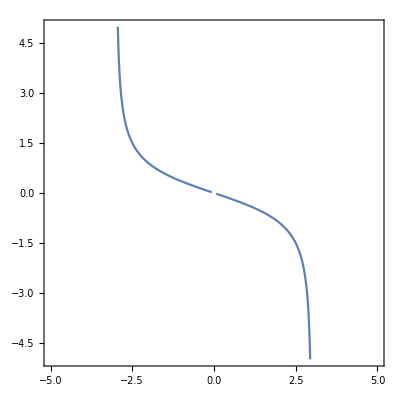

```mathematica
ContourPlot[df[x,y,3]==0,{x,-5,5},{y,-5,5},PlotPoints->100]
```

```mathematica
f[x_,y_,{{x0_,y0_},r_}]:=(x-x0)^2+(y-y0)^2-r^2
```

```mathematica
l[{a1_,b1_},{a2_,b2_}]:=√((a2-a1)^2+(b2-b1)^2)
```

```mathematica
v[{a1_,b1_},{a2_,b2_}]:={a2-a1,b2-b1}
```

```mathematica
dfy[x_,r_]:=-x/(√(r^2-x^2))
```

```mathematica
fr[al_,{{x0_,y0_},r_}]:={r Cos[al]+x0,r Sin[al]+y0}
```

```mathematica
or1={0,0};or2={10,0};
```

```mathematica
r1={or1,3};r2={or2,5};
al=Pi/20.;bet = Pi/30.;
```

```mathematica
Clear[al,bet]
```

```mathematica
a=fr[al+Pi/2,r1];b=fr[Pi/2-bet,r2];
```

```mathematica
p={a,b};
```

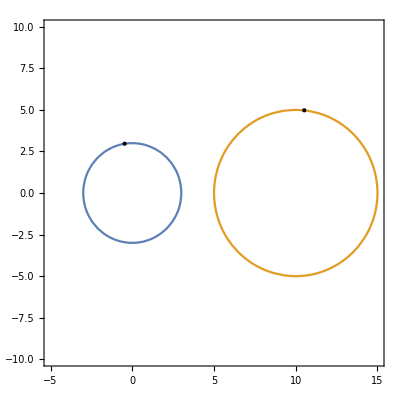

```mathematica
ContourPlot[Evaluate[(f[x,y,#]==0)&/@{r1,r2}],{x,-5,15},{y,-10,10},Epilog->Point[p]]
```

```mathematica
ab=Norm[v[a,b]]
```

11.1741

```mathematica
rs=ab/2 1/Sin[(al+bet)/2]
```

42.8042

```mathematica
o={x,y}/.Solve[{f[x,y,{a,rs}]==0,f[x,y,{b,rs}]==0},{x,y}][[2]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{12.6587,-37.7782}

```mathematica
o1=#1+#3 v[#1,#2]/Norm[v[#1,#2]]&[a,or1, R1];
o2=#1+#3 v[#1,#2]/Norm[v[#1,#2]]&[b,or2, R2];
```

```mathematica
R1=rs Sin[gam/2]/Sin[(al-bet+gam)/2]
R2=rs Sin[(al-bet+gam)/2]/Sin[bet-gam/2]
```

```mathematica
o1
```

{-0.469303+0.156434 R1,2.96307-0.987688 R1}

```mathematica
o2
```

{10.5226-0.104528 R2,4.97261-0.994522 R2}

```mathematica
q=o1 + R1 v[o1,o2]/Norm[v[o1,o2]]
```

{-0.469303+0.156434 R1+(R1 (10.9919-0.156434 R1-0.104528 R2))/(√(Abs[2.00954+0.987688 R1-0.994522 R2]^2+Abs[10.9919-0.156434 R1-0.104528 R2]^2)),2.96307-0.987688 R1+(R1 (2.00954+0.987688 R1-0.994522 R2))/(√(Abs[2.00954+0.987688 R1-0.994522 R2]^2+Abs[10.9919-0.156434 R1-0.104528 R2]^2))}

```mathematica
gam=VectorAngle[v[o,q],v[o,a]]
```

ArcCos[(0.0233622 (40.7413 (40.7413-0.987688 R1+(R1 (2.00954+0.987688 R1-0.994522 R2))/(√(Abs[2.00954+0.987688 R1-0.994522 R2]^2+Abs[10.9919-0.156434 R1-0.104528 R2]^2)))-13.128 (-13.128+0.156434 R1+(R1 (10.9919-0.156434 R1-0.104528 R2))/(√(Abs[2.00954+0.987688 R1-0.994522 R2]^2+Abs[10.9919-0.156434 R1-0.104528 R2]^2)))))/(√(Abs[40.7413-0.987688 R1+(R1 (2.00954+0.987688 R1-0.994522 R2))/(√(Abs[2.00954+0.987688 R1-0.994522 R2]^2+Abs[10.9919-0.156434 R1-0.104528 R2]^2))]^2+Abs[-13.128+0.156434 R1+(R1 (10.9919-0.156434 R1-0.104528 R2))/(√(Abs[2.00954+0.987688 R1-0.994522 R2]^2+Abs[10.9919-0.156434 R1-0.104528 R2]^2))]^2))]

```mathematica
NSolve[{R1==rs Sin[gam/2]/Sin[(al-bet+gam)/2],
R2==rs Sin[(al-bet+gam)/2]/Sin[bet-gam/2]},{R1,R2}]
```

$Aborted

```mathematica
l[x_,y_,{{a1_,b1_},{a2_,b2_}}]:=(x-a1)/(a2-a1)-(y-b1)/(b2-b1)
```

```mathematica
Solve[{l[x,y,{o1,o2}]==0,f[x,y,{o,rs}]==0},{x,y}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

## forward

```mathematica
f[x_,y_,{{x0_,y0_},r_}]:=(x-x0)^2+(y-y0)^2-r^2
```

```mathematica
v[{a1_,b1_},{a2_,b2_}]:={a2-a1,b2-b1}
```

```mathematica
fr[al_,{{x0_,y0_},r_}]:={r Cos[al]+x0,r Sin[al]+y0}
```

```mathematica
or1={0,0};or2={25,0};
```

```mathematica
r1={or1,0.5};r2={or2,3.5};
al=Pi/6.;bet = Pi/3.;gam=Pi/3.;
```

```mathematica
2 Pi + bet - al
```

6.80678

```mathematica
2 bet
```

2.0944

```mathematica
If[2 Pi + bet - al>gam>2 bet,Print["Ok"],Print["Bad"]]
```

Bad

```mathematica
gam
```

1.0472

```mathematica
a=fr[al+Pi/2,r1];b=fr[Pi/2-bet,r2];
```

```mathematica
p={a,b};
```

```mathematica
v[a,b]
```

{28.2811,1.31699}

```mathematica
a
```

{-0.25,0.433013}

```mathematica
b
```

{28.0311,1.75}

```mathematica
ab=Norm[v[a,b]]
```

28.3117

```mathematica
rs=ab/2 1/Sin[(al+bet)/2]
```

20.0194

```mathematica
R1=rs Sin[gam/2]/Sin[(al-bet+gam)/2]
R2=rs Sin[(al-bet+gam)/2]/Sin[bet-gam/2]
```

38.6746

10.3628

```mathematica
o1=#1+#3 v[#1,#2]/Norm[v[#1,#2]]&[a,or1, R1]
o2=#1+#3 v[#1,#2]/Norm[v[#1,#2]]&[b,or2, R2]
```

{19.0873,-33.0601}

{19.0566,-3.43141}

```mathematica
rR1={o1,R1}
rR2={o2,R2}
```

{{19.0873,-33.0601},38.6746}

{{19.0566,-3.43141},10.3628}

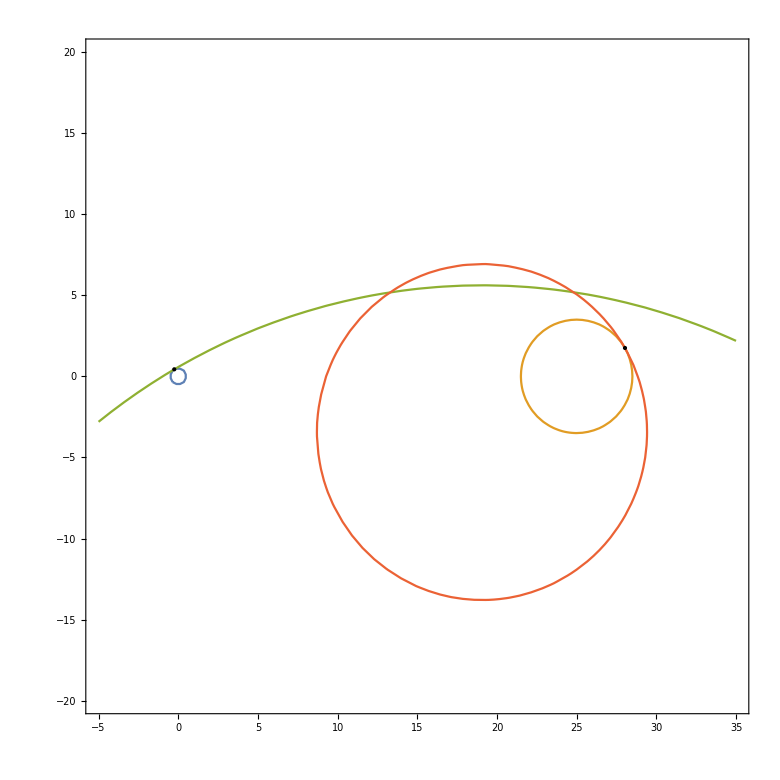

```mathematica
ContourPlot[Evaluate[(f[x,y,#]==0)&/@{r1,r2,rR1,rR2}],{x,-5,35},{y,-20,20},Epilog->Point[p]]
```

zbs

```mathematica
f[x_,y_,{{x0_,y0_},r_}]:=(x-x0)^2+(y-y0)^2-r^2
```

```mathematica
v[{a1_,b1_},{a2_,b2_}]:={a2-a1,b2-b1}
```

```mathematica
fr[al_,{{x0_,y0_},r_}]:={r Cos[al]+x0,r Sin[al]+y0}
```

```mathematica
or1={0,0};or2={25,0};
o1o2=Norm[or2-or1]
```

25

```mathematica
r1=5;r2=2;
rr1={or1,r1};rr2={or2,r2};
al=-Pi/6. 1.55;bet = -Pi/3. 1;gam=-Pi/3. .5;
```

```mathematica
2 bet
bet - al
```

-2.0944

-0.235619

```mathematica
gam
```

-0.523599

```mathematica
star=r1 Sin[Pi/2-al]-r2 Sin[Pi/2-bet];
```

```mathematica
fi = ArcCos[star/o1o2];
a=fr[al+fi,rr1]
b=fr[fi-bet,rr2]
```

{3.94569,3.07108}

{23.3739,1.16439}

```mathematica
p={a,b};
```

```mathematica
ab=Norm[v[a,b]]
```

19.5215

```mathematica
rs=ab/2 1/Sin[(al+bet)/2]
```

-12.1819

```mathematica
R1=rs Sin[gam/2]/Sin[(al-bet+gam)/2]
R2=rs Sin[(al+bet-gam)/2]/Sin[bet-gam/2]
```

-21.9726

-10.6656

```mathematica
o1=#1+#3 v[#1,#2]/Norm[v[#1,#2]]&[a,or1, R1]
o2=#1+#3 v[#1,#2]/Norm[v[#1,#2]]&[b,or2, R2]
```

{21.2851,16.567}

{14.7022,7.37385}

```mathematica
rR1={o1,R1}
rR2={o2,R2}
```

{{21.2851,16.567},-21.9726}

{{14.7022,7.37385},-10.6656}

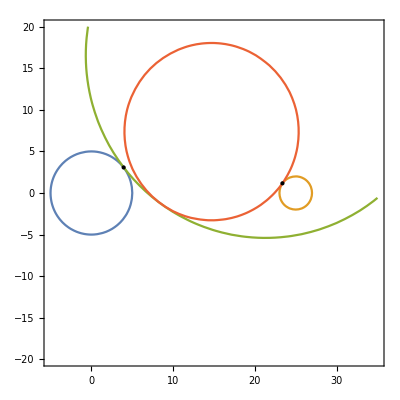

```mathematica
ContourPlot[Evaluate[(f[x,y,#]==0)&/@{rr1,rr2,rR1,rR2}],{x,-5,35},{y,-20,20},Epilog->Point[p]]
```

```mathematica
m[fi_]:= {{Cos[fi],-Sin[fi]},{Sin[fi],Cos[fi]}}
```

```mathematica
{1,0}.m[-Pi/2]
```

{0,1}